```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
Get["Spectra/ElectronSpectrum.m"]
Get["Spectra/ProtonSpectrumNachtmann.m"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

### settings

```mathematica
SeedRandom[1000]
```

```mathematica
SpectrumDir="~/Documents/Mma_Spectra_1e8_2e3_Glueck93_thMax45/";
```

```mathematica
TotalNumber=10*10^7;
PackageSize=2*10^3;
DataSets=TotalNumber/PackageSize
```

50000

```mathematica
ThetaMax=Pi/4;
```

```mathematica
SetDirectory[SpectrumDir]
```

/home/waleed/Documents/Mma_Spectra_1e8_2e3_Glueck93_thMax45

```mathematica
CloseKernels[]
```

{}

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

## Energy-Spectra definition

```mathematica
?weNormed
```

```mathematica
ProtonSpectrumPDF=ProbabilityDistribution[dwdtNormed[T,-0.105],{T,0,tpMax}]
```

ProbabilityDistribution[0.00111418 (0.0335173 (1-0.156106/(1-0.00112341 x))^2 √x (4 (1+0.156106/(1-0.00112341 x))-(0.00149788 (0.843894-0.00112341 x) x)/(1-0.00112341 x))-0.00351931 (1-0.156106/(1-0.00112341 x))^2 √x (4 (1+0.156106/(1-0.00112341 x)-2 (1-0.00112341 x))-(0.00149788 (0.843894-0.00112341 x) x)/(1-0.00112341 x))),{x,0,751.192}]

```mathematica
|
```

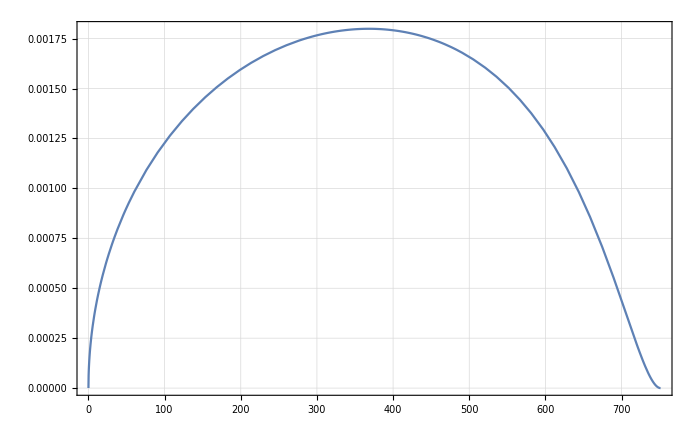

```mathematica
Plot[PDF[ProtonSpectrumPDF,T],{T,0,tpMax}]
```

```mathematica
NIntegrate[PDF[ProtonSpectrumPDF,T],{T,0,tpMax}]
```

0.999904

## ThetaDist

```mathematica
ThetaMax
```

π/4

```mathematica
ThetaMaxDegree=ThetaMax/Pi*180.
```

45.

```mathematica
ThetaNorm=Integrate[Sin[th/180*Pi],{th,0,ThetaMaxDegree}]
```

16.7815

```mathematica
ThetaPDF=ProbabilityDistribution[Sin[th/180.*Pi],{th,0,ThetaMaxDegree},Method->"Normalize"]
```

ProbabilityDistribution[0.0595893 Sin[0.0174533 x],{x,0,45.}]

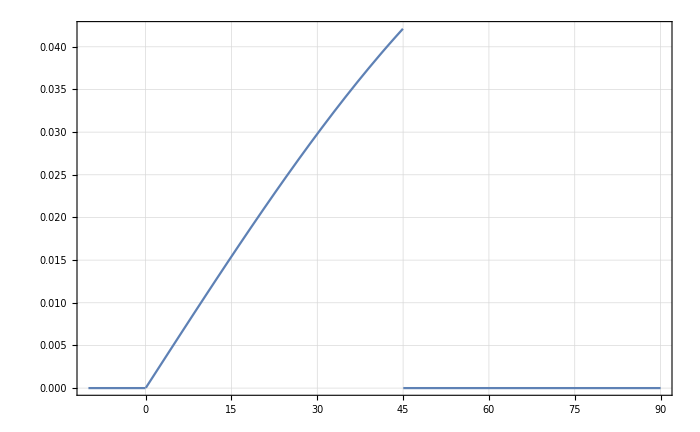

```mathematica
Plot[PDF[ThetaPDF,x],{x,-10,90}]
```

```mathematica
RandomVariate[ThetaPDF,10]
```

{43.6904,36.966,42.1034,16.9862,21.5728,39.4446,21.6823,39.5781,31.0314,28.4791}

```mathematica
testdata=RandomVariate[ThetaPDF,10^3];
```

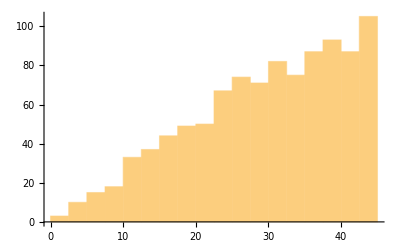

```mathematica
Histogram[testdata,{0,45,2.5}]
```

## Phi Uniform

```mathematica
PhiPDF=UniformDistribution[{0,360.}]
```

UniformDistribution[{0,360.}]

## create data

## electron energy also in eV

```mathematica
t0=AbsoluteTime[];
EeList=ParallelTable[RandomVariate[ElectronSpectrumPDF,PackageSize]-me,{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[33553@193.170.93.100,42205@193.170.93.100,235,16].

Kernels::rdead: Subkernel connected through KernelObject[8,193.170.93.100] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {11} assigned to KernelObject[8,193.170.93.100,<defunct>].

LinkObject::linkn: Argument LinkObject[33553@193.170.93.100,42205@193.170.93.100,235,16] in LinkClose[LinkObject[33553@193.170.93.100,42205@193.170.93.100,235,16]] has an invalid LinkObject number; the link may be closed.

OptionValue::nodef: Unknown option KernelSpeed for LightweightGridClient`RemoteKernelOpen.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[8,193.170.93.100,<defunct>] resurrected as KernelObject[15,193.170.93.100].

LinkObject::linkd: Unable to communicate with closed link LinkObject[34357@193.170.93.100,39593@193.170.93.100,236,17].

Kernels::rdead: Subkernel connected through KernelObject[9,193.170.93.100] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {60} assigned to KernelObject[9,193.170.93.100,<defunct>].

LinkObject::linkn: Argument LinkObject[34357@193.170.93.100,39593@193.170.93.100,236,17] in LinkClose[LinkObject[34357@193.170.93.100,39593@193.170.93.100,236,17]] has an invalid LinkObject number; the link may be closed.

LaunchKernels::clone: Kernel KernelObject[9,193.170.93.100,<defunct>] resurrected as KernelObject[16,193.170.93.100].

LinkObject::linkd: Unable to communicate with closed link LinkObject[42453@193.170.93.100,46395@193.170.93.100,237,18].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[10,193.170.93.100] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {72} assigned to KernelObject[10,193.170.93.100,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "193.170.93.100".

LaunchKernels::clone: Kernel KernelObject[10,193.170.93.100,<defunct>] resurrected as KernelObject[17,193.170.93.100].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject[35093@193.170.93.100,35941@193.170.93.100,234,15] in LinkClose[LinkObject[35093@193.170.93.100,35941@193.170.93.100,234,15]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

13505.99858

```mathematica
EeList[[1,1;;10]]
```

{357829.,212773.,500251.,492669.,630753.,320610.,287717.,443733.,616803.,91494.6}

### proton Ekin

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[1,193.170.93.93,<defunct>],KernelObject[2,193.170.93.93,<defunct>],KernelObject[3,193.170.93.93,<defunct>],KernelObject[4,193.170.93.93,<defunct>],KernelObject[5,193.170.93.93,<defunct>],KernelObject[6,193.170.93.93,<defunct>],KernelObject[14,local,<defunct>],KernelObject[15,193.170.93.100,<defunct>],KernelObject[16,193.170.93.100,<defunct>],KernelObject[17,193.170.93.100,<defunct>],KernelObject[20,193.170.93.100,<defunct>],KernelObject[22,local,<defunct>],KernelObject[23,local,<defunct>],KernelObject[24,193.170.93.100,<defunct>]}

{KernelObject[25,193.170.93.93],KernelObject[26,193.170.93.93],KernelObject[27,193.170.93.93],KernelObject[28,193.170.93.93],KernelObject[29,193.170.93.93],KernelObject[30,193.170.93.93],KernelObject[31,193.170.93.100],KernelObject[32,193.170.93.100],KernelObject[33,193.170.93.100],KernelObject[34,193.170.93.100],KernelObject[35,193.170.93.100],KernelObject[36,local],KernelObject[37,local]}

```mathematica
t0=AbsoluteTime[];
TpList=ParallelTable[RandomVariate[ProtonSpectrumPDF,PackageSize],{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

397.743586

## Theta

```mathematica
ClearAll[ThetaList]
```

```mathematica
t0=AbsoluteTime[];
ThetaList=ParallelTable[RandomVariate[ThetaPDF,PackageSize],{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

66.614163

```mathematica
ThetaList[[1,1;;10]]
```

{35.7078,36.2308,37.7103,28.2211,17.4618,24.5143,36.3809,30.7473,25.8904,44.2258}

```mathematica
ThetaList//Dimensions
```

{50000,2000}

### takes 1513s for 3 cores,

## Phi

```mathematica
t0=AbsoluteTime[];
PhiList=ParallelTable[RandomVariate[PhiPDF,PackageSize],{DataSets}];
t1=AbsoluteTime[];
t1-t0
```

0.966833

# data check

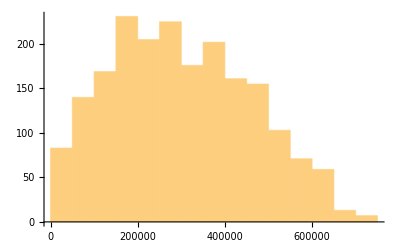

```mathematica
Histogram[EeList[[1]]]
```

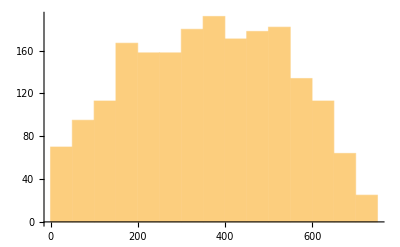

```mathematica
Histogram[TpList[[1]]]
```

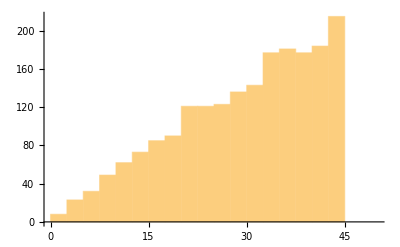

```mathematica
Histogram[ThetaList[[1]],{0,50,2.5}]
```

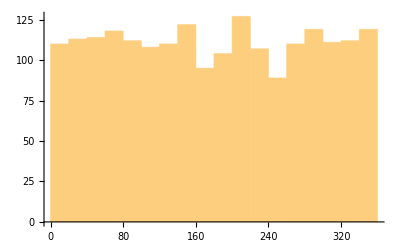

```mathematica
Histogram[PhiList[[1]]]
```

# export

```mathematica
Which[PackageSize==10^4,PackageString="1e4_",PackageSize==2*10^3,PackageString="2e3_"]
```

2e3_

```mathematica
DataSets
```

50000

```mathematica
CloseKernels[]
LaunchKernels[2]
```

{KernelObject[25,193.170.93.93,<defunct>],KernelObject[26,193.170.93.93,<defunct>],KernelObject[27,193.170.93.93,<defunct>],KernelObject[28,193.170.93.93,<defunct>],KernelObject[29,193.170.93.93,<defunct>],KernelObject[30,193.170.93.93,<defunct>],KernelObject[31,193.170.93.100,<defunct>],KernelObject[32,193.170.93.100,<defunct>],KernelObject[33,193.170.93.100,<defunct>],KernelObject[34,193.170.93.100,<defunct>],KernelObject[35,193.170.93.100,<defunct>],KernelObject[36,local,<defunct>],KernelObject[37,local,<defunct>]}

{KernelObject[38,local],KernelObject[39,local]}

```mathematica
ParallelTable[
Export["Spectra"<>PackageString<>ToString[i-1]<>".txt",Transpose[{SetPrecision[ThetaList[[i]],10],SetPrecision[PhiList[[i]],10],SetPrecision[TpList[[i]],10],SetPrecision[TpList[[i]],10]}],"Table"],
{i,DataSets}];
```

### takes 2726s for 5e7_2e3

### 2992s for 10e7_2e7, 2 cores

```mathematica
Directory[]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_5e7_2e3

# DumpSaving

```mathematica
DumpSaveDir=SpectrumDir
```

~/FerencSource+Spectra/Mma_Spectra_1e8_2e3_Glueck93_thMax45

```mathematica
SetDirectory[DumpSaveDir]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_1e8_2e3_Glueck93_thMax45

```mathematica
DumpSave["EeList.mx",EeList];
```

```mathematica
DumpSave["TpList.mx",TpList];
```

```mathematica
DumpSave["ThetaList.mx",ThetaList];
```

```mathematica
DumpSave["PhiList.mx",PhiList];
```

# Dump loading

### we can also load from dump save

```mathematica
DumpLoadDir="~/FerencSource+Spectra/Mma_Spectra_5e7_1e4";
```

```mathematica
SetDirectory[DumpLoadDir]
```

/home/dmoser/FerencSource+Spectra/Mma_Spectra_5e7_1e4

```mathematica
ClearAll[EeList]
```

```mathematica
Get["EeList.mx"]
```

```mathematica
EeList//Dimensions
```

{5000,10000}

```mathematica
EeList=Map[Partition[#,PackageSize]&,EeList];
```

```mathematica
EeList//Dimensions
```

{5000,5,2000}

```mathematica
EeList=Flatten[EeList,1];
```

```mathematica
EeList//Dimensions
```

{25000,2000}

### we can also load from dump save

```mathematica
ClearAll[EeList]
```

```mathematica
Get["TpList.mx"]
```

```mathematica
TpList//Dimensions
```

{5000,10000}

```mathematica
TpList=Map[Partition[#,PackageSize]&,TpList];
```

```mathematica
TpList//Dimensions
```

{5000,5,2000}

```mathematica
TpList=Flatten[TpList,1];
```

```mathematica
TpList//Dimensions
```

{25000,2000}

### we can also load from dump save

```mathematica
ClearAll[ThetaList]
```

```mathematica
Get["ThetaList.mx"]
```

Get::noopen: Cannot open ThetaList.mx.

$Failed

```mathematica
ThetaList//Dimensions
```

{25000,2000}

```mathematica
ThetaList=Map[Partition[#,PackageSize]&,ThetaList];
```

```mathematica
ThetaList//Dimensions
```

{5000,5,2000}

```mathematica
ThetaList=Flatten[ThetaList,1];
```

```mathematica
ThetaList//Dimensions
```

{25000,2000}

### we can also load from dump save

```mathematica
ClearAll[EeList]
```

```mathematica
Get["PhiList.mx"]
```

```mathematica
PhiList//Dimensions
```

{5000,10000}

```mathematica
PhiList=Map[Partition[#,PackageSize]&,PhiList];
```

```mathematica
PhiList//Dimensions
```

{5000,5,2000}

```mathematica
PhiList=Flatten[PhiList,1];
```

```mathematica
PhiList//Dimensions
```

{25000,2000}